# Evolved Gradient Discrimination

## Import

### Setup and libraries

```mathematica
ClearAll["Global`*"]
Clear["Global`*"]
Needs["PlotLegends`"]
<<"~thomasbuhrmann/Code/Mathematica/Dynamica/Dynamica.m";
```

Dynamica (Version 1.0.5 - 12/6/11), Copyright(c) 1993-2011 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

### Import data

```mathematica
dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/DerivativeOnly/HighFrameRateInc/12_07_05__18_03_56"; 
dt=1/200;
(*dirName = "/Users/thomasbuhrmann/Experiments/eSMCs/DerivativeOnly/12_06_25__14_58_12"; dt=0.02;*)
SetDirectory[dirName];
genFit=Import["Generalization.txt", "Table"];
data = Import["State.txt", "Table"];
stateNames=data[[1]]
state = data[[2;;-2]];
numStates=Dimensions[stateNames];
numData=Length[state]

fitXml = Import["GA_Progress.xml"];
bestFitness=Cases[fitXml,XMLElement["Generation",{_,"BestFitness"->fit_,_},___]->fit,Infinity];
avgFitness=Cases[fitXml,XMLElement["Generation",{_,_,"AverageFitness"->fit_},___]->fit,Infinity];
bestFitness=ToExpression[bestFitness];
avgFitness=ToExpression[avgFitness];
```

{Angle,AngularVel,NeuralExtInput0,NeuralExtInput1,NeuralExtInput2,NeuralOutput0,NeuralOutput1,NeuralOutput2,NeuralState0,NeuralState1,NeuralState2,PosX,PosY,Sensor,SensorDer,VelX,VelY}

40000

## Functions

```mathematica
TtoI[time_]:=Floor[time/dt];
NtoI[name_]:=Position[stateNames, name][[1,1]];
NtoD[name_,t0_,tn_]:=Table[state[[i,NtoI[name]]],{i,t0,tn}];
time = Range[0,100.0,dt];
padds={{20,40},{20,20}};
plotOptions = {PlotJoined->True, ImagePadding->padds};

TimeTrajectory[name_,t1_,t2_]:=Transpose[{time[[1;;(t2-t1+1)]],NtoD[name,t1,t2]}];

TimeTrajectory2d[name1_, name2_,t0_,tn_]:=Transpose[{time[[1;;tn-t0+1]],NtoD[name1,t0,tn],NtoD[name2,t0,tn]}];

PhaseTrajectory[name1_, name2_,t0_,tn_,m1_:1,m2_:1]:=Transpose[{m1*NtoD[name1,t0,tn],m2*NtoD[name2,t0,tn]}];

PhaseTrajectory3d[name1_, name2_,name3_,t0_,tn_,m1_:1,m2_:1,m3_:1]:=Transpose[{m1*NtoD[name1,t0,tn],m2*NtoD[name2,t0,tn],m3*NtoD[name3,t0,tn]}];

TimePlot[name_,t0_,tn_,options_:{}] := ListLinePlot[TimeTrajectory[name,t0,tn], Join[plotOptions,options],AxesLabel->{"time",name}];

TimePlot2d[name1_,name2_,t0_,tn_,options_:{}]:=Graphics3D[{Line[TimeTrajectory2d[name1,name2,t0,tn],VertexColors->1-Range[0,1,1/(tn-t0)]]},options,AxesLabel->{"time",name1,name2}];

PhasePlot[name1_,name2_,t0_,tn_,options_:{},m1_:1,m2_:1]:=Graphics[Line[PhaseTrajectory[name1,name2,t0,tn,m1,m2],VertexColors->1-Range[0,1,1/(tn-t0)]],Axes->True,AxesLabel->{name1,name2},options,AspectRatio->1.0];

PhasePlot3d[name1_,name2_,name3_,t0_,tn_,options_:{},m1_:1,m2_:1,m3_:1]:=Graphics3D[Line[PhaseTrajectory3d[name1,name2,name3,t0,tn,m1,m2,m3],VertexColors->1-Range[0,1,1/(tn-t0)]],Axes->True,AxesLabel->{name1,name2},options,AspectRatio->1.0];

Colorbar[colorFunction_: Automatic,min_:0,max_:1,divs_: 25]:=DensityPlot[y,{x,0,1},{y,min,max},AspectRatio->10,PlotRangePadding->0,PlotPoints->{2,divs},MaxRecursion->0,FrameTicks->{None,Automatic,None,None},ColorFunction->colorFunction];
```

## Task

Analyse the Gaussian function and how its gradient changes for different amplitudes and widths.

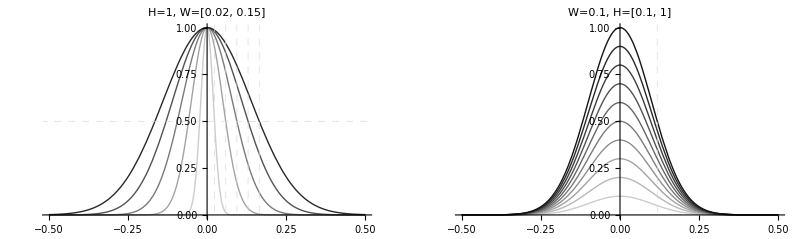

{23}

{25}

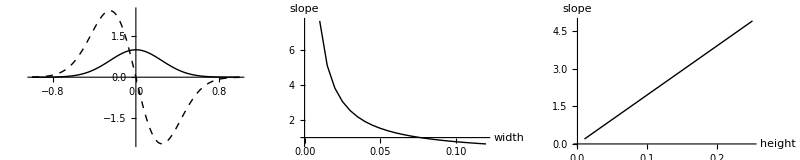

```mathematica
Gaus[x_,h_,w_]:=h Exp[-x^2/(2 w^2)];
GausDx[x_,h_,w_]:=-h/w^2 x Exp[-x^2/(2 w^2)];
HWHM[w_]:=0.5*2.3548*w;

widthRange=Range[0.02,0.15,0.03];
heightRange=Range[0.1,1,0.1];
hwhm=HWHM[widthRange];


GrayLevelTable[steps_]:=Table[GrayLevel[i],{i,0.8,0.0,-0.8/steps}];
widthColors=GrayLevelTable[Length[widthRange]];
heightColors=GrayLevelTable[Length[heightRange]];

gaussWidthPlot=Plot[Evaluate[Table[Gaus[v,1,width],{width,widthRange}]],{v,-0.5,0.5},PlotRange->All,PlotStyle->widthColors,GridLines->{hwhm,{0.5}},GridLinesStyle->Dashed,PlotLabel->"H=1, W=[0.02, 0.15]"];

gaussHeightPlot=Plot[Evaluate[Table[Gaus[v,height,0.1],{height,heightRange}]],{v,-0.5,0.5},PlotRange->All,PlotStyle->heightColors,GridLines->{{HWHM[0.1]},{}},GridLinesStyle->Dashed,PlotLabel->"W=0.1, H=[0.1, 1]"];

gaussDxPlot=Show[Plot[Gaus[x,1,0.25],{x,-1,1},PlotStyle->Black],Plot[GausDx[x,1,0.25],{x,-1,1},PlotStyle->{Black,Dashed}],PlotRange->All];

GraphicsRow[{gaussWidthPlot,gaussHeightPlot},ImageSize->800]

(* Plot slope of gaussian at hwhm for different widths *)
widthRange=Range[0.01,0.12,0.005]; Dimensions[widthRange]
heightRange=Range[0.01,0.25,0.01];Dimensions[heightRange]
slopes=Table[GausDx[HWHM[width],0.13,width],{width,widthRange}];
widthSlopePlot=ListLinePlot[Transpose[{widthRange,Abs[slopes]}],AxesLabel->{width,slope},PlotStyle->Black];

(* Plot slope of gaussian at hwhm for different heights *)
slopes=Table[GausDx[HWHM[0.03],height,0.03],{height,heightRange}];
heightSlopePlot=ListLinePlot[Transpose[{heightRange,Abs[slopes]}],AxesLabel->{height,slope},PlotStyle->Black];

GraphicsRow[{gaussDxPlot,widthSlopePlot,heightSlopePlot},ImageSize->800]
```

### A&A-style SMC for Gaussian

Shows for every position x (with Gaussian centred at origin), the difference in sensor reading as one moves a distance dx away from x. This tries to replicate the diagrams of Alex and Andreas, in which for a given motor command (a distance moved in a certain direction), the plot shows whether one will encounter a sensor reading s’ when the current reading is s.

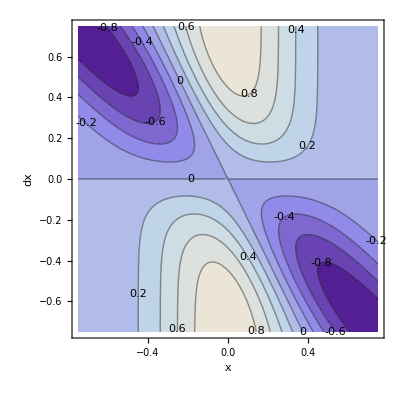

```mathematica
ww=0.25;hh=1;
xLim=0.75;
dxLim=0.75;

smc3d=Plot3D[Gaus[x,hh,ww]-Gaus[x+dx,hh,ww],{x,-xLim,xLim},{dx,-dxLim,dxLim},AxesLabel->{"x","dx"}];
smcCtr=ContourPlot[Gaus[x,hh,ww]-Gaus[x+dx,hh,ww],{x,-xLim,xLim},{dx,-dxLim,dxLim},ContourLabels->True,FrameLabel->{"x","dx"}];
GraphicsRow[{smc3d,smcCtr},ImageSize->800]
```

Another version: here we show for every possible sensor reading s(t) (instead of position), the next sensor reading after moving a certain amount in a given direction (to the right, but left is symmetric). Since every possible sensor reading occurs exactly twice with the Gaussian, the solid lines indicate those initial sensor readings corresponding to the right (positive) side of the Gaussian, and the dashed lines those on the left. Darker lines indicated smaller movements away from initial position.

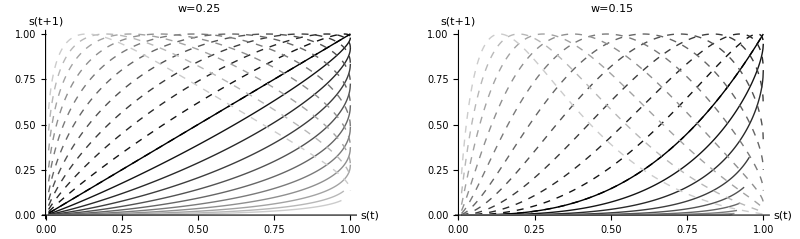

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

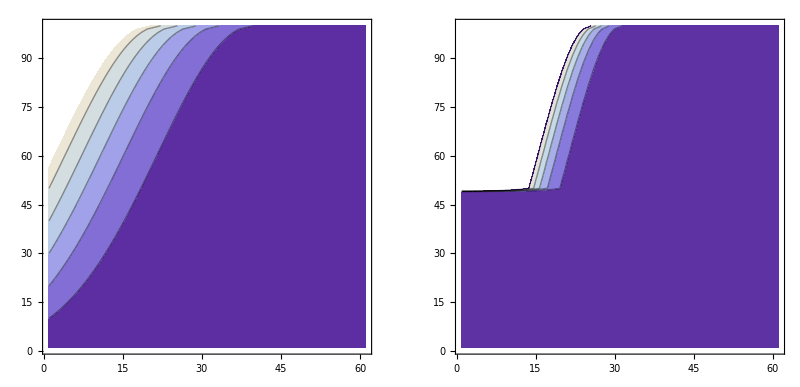

```mathematica
(* Find the positions where the Gaussian takes on values 0.1,..,1, only right side *)
positions=Table[FindRoot[Gaus[x,1.0,0.25]==val,{x,0.001,0,1}],{val,0.01,1,0.001}] ;
positions=x/.%;

(* Now move a certain amount away from these positions and find new values of Gaussian *)
PlotSMC[h_,w_,mv_,col_:0]:=Show[
ListLinePlot[Transpose[{Range[0.01,1,0.001],Gaus[positions+mv,h,w]}],PlotStyle->GrayLevel[col],AxesLabel->{"s(t)","s(t+1)"}],
ListLinePlot[Transpose[{Range[0.01,1,0.001],Gaus[-positions+mv,h,w]}],PlotStyle->{GrayLevel[col],Dashed}],
PlotRange->All
];

moves=Range[0,0.5,0.5/10];
wideSMC=Show[Table[PlotSMC[1,0.25,move,0.8*(move/Max[moves])],{move,moves}],PlotLabel->"w=0.25"];
narrowSMC=Show[Table[PlotSMC[1,0.15,move,0.8*(move/Max[moves])],{move,moves}],PlotLabel->"w=0.15"];
GraphicsRow[{wideSMC,narrowSMC}]

GausPos[y_,h_,w_]:=FindRoot[Gaus[x,h,w]==y,{x,0.001,0,1}] [[1,2]];
density =Table[Gaus[GausPos[val,1,0.18]+mv,1.0,0.18],{val,0.01,1,0.01},{mv,0,0.6,0.01}];
density2 =Table[Gaus[GausPos[val,1,0.1]+mv,1.0,0.1],{val,0.01,1,0.01},{mv,0,0.6,0.01}];
GraphicsRow[{ListContourPlot[density],ListContourPlot[density2]}]
```

## Fitness

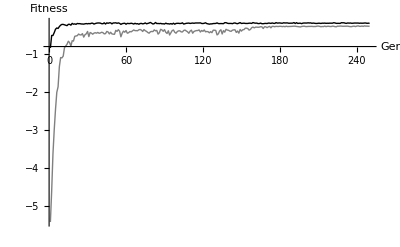

-0.163453

```mathematica
bestFitP =ListLinePlot[bestFitness,PlotStyle->Black,PlotRange->All,ImageSize->400,AxesLabel->{Gen, Fitness}];
avgFitP =ListLinePlot[avgFitness,PlotStyle->Gray,PlotRange->All,ImageSize->400];
Show[bestFitP, avgFitP]
maxFit = Max[bestFitness]
```

## Generalization

Fitness (distance from center of Gaussian) as a function of the height (horizontal) and width (vertical) of the Gaussian. Only one Gaussian was presented in these trials. For each combination of width and height, the Gaussian was presented at 10 locations, uniformly distributed over the horizontal field of view (-0.4, 0.4) and at a distance of 0.4 (the maximum sensor distance). During evolution only two widths were encountered: 0.03 and 0.08, while the amplitude varied around 0.13 +- 50%.

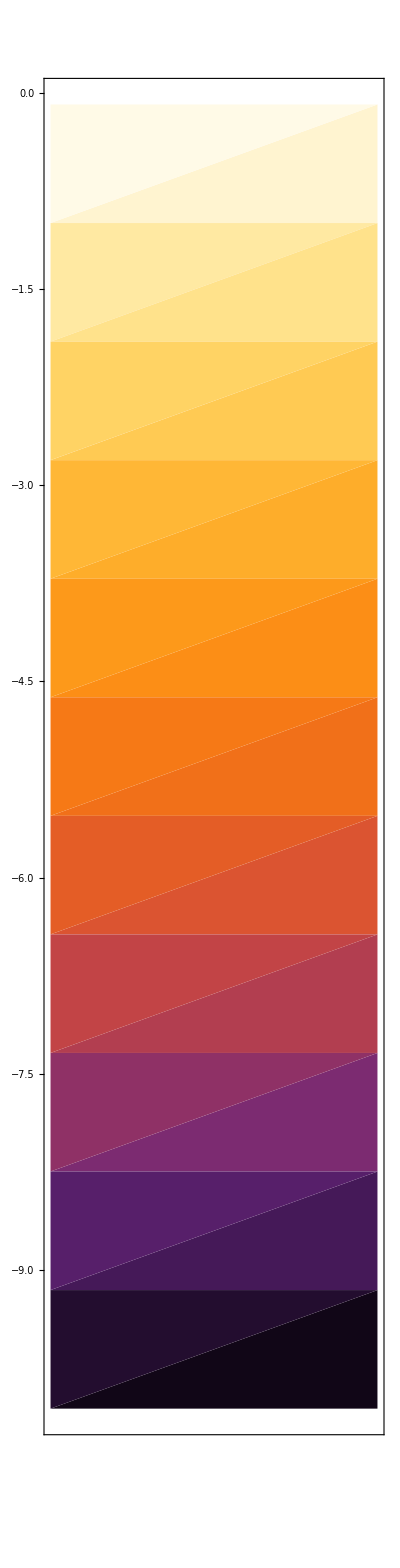
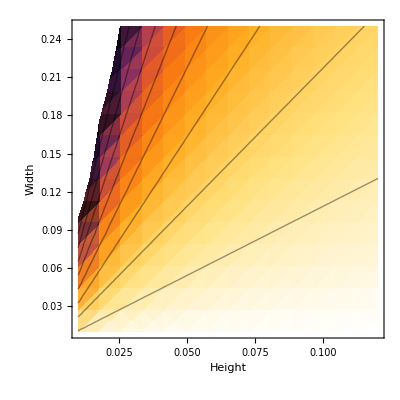
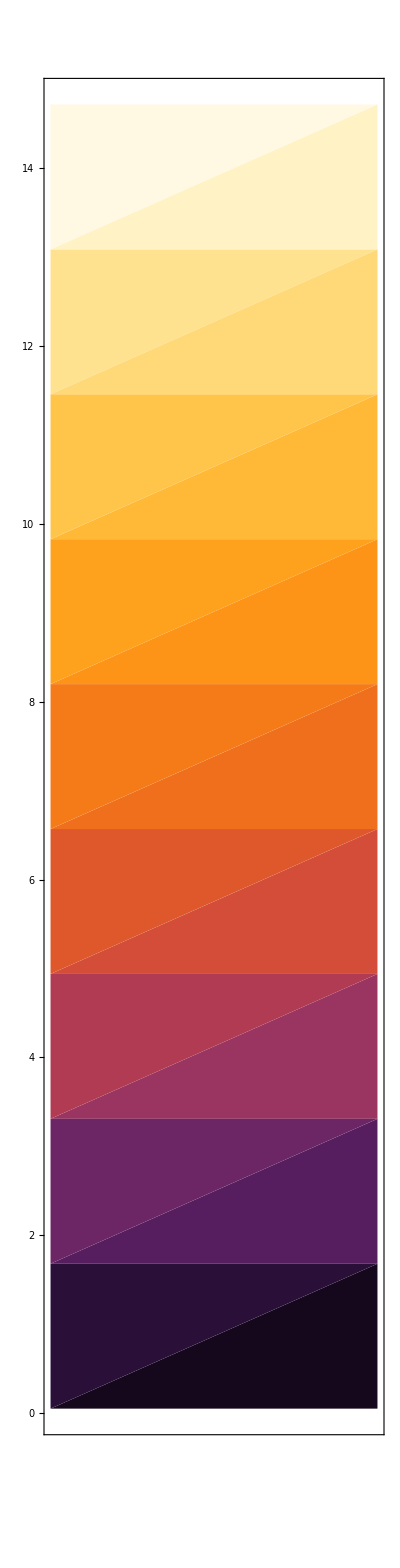
-Graphics--Graphics- -Graphics--Graphics-

```mathematica
slopes2d=Transpose[Abs[Table[GausDx[HWHM[width],height,width],{height,heightRange},{width,widthRange}]]];
maxSlope=Round[Max[slopes2d],0.01];
minSlope=Round[Min[slopes2d],0.01];
color="SunsetColors";

slopeDensity=DensityPlot[GausDx[HWHM[width],height,width],{width,Min[widthRange],Max[widthRange]},{height,Min[heightRange],Max[heightRange]},ColorFunction->ColorData[color],FrameLabel->{Height,Width}];

slopeContours=ContourPlot[GausDx[HWHM[width],height,width],{width,Min[widthRange],Max[widthRange]},{height,Min[heightRange],Max[heightRange]},ContourShading->None,Contours->8,(*ContourStyle->Directive[Black,Dashed],*)ColorFunction->ColorData[color],FrameLabel->{Height,Width}];

slopeCombined=Show[slopeDensity,slopeContours];

slopeDensityPlot=With[{size=300},Row[Show[#,ImageSize->{Automatic,size},ImagePadding->{{25,5},{20,5}}]&/@{slopeCombined,Colorbar[ColorData[color],minSlope,maxSlope,10]}]];

genFitMin=Round[Min[genFit],0.001];
genFitMax=Round[Max[genFit],0.001];
numContours=10;

fitdens=ListDensityPlot[genFit,DataRange->{{0.01,0.2476},{0.01,0.1189}},ColorFunction->ColorData[color],ColorFunctionScaling->True,InterpolationOrder->1,FrameLabel->{"Height","Width"}];

fitDensityPlot=With[{size=300},Row[Show[#,ImageSize->{Automatic,size},ImagePadding->{{25,5},{20,5}}]&/@{fitdens,Colorbar[ColorData[color],genFitMin,genFitMax,12]}]];

fitDensityPlot slopeDensityPlot
```

The fitness density plot resembles features of the slope density plot.

## Time series

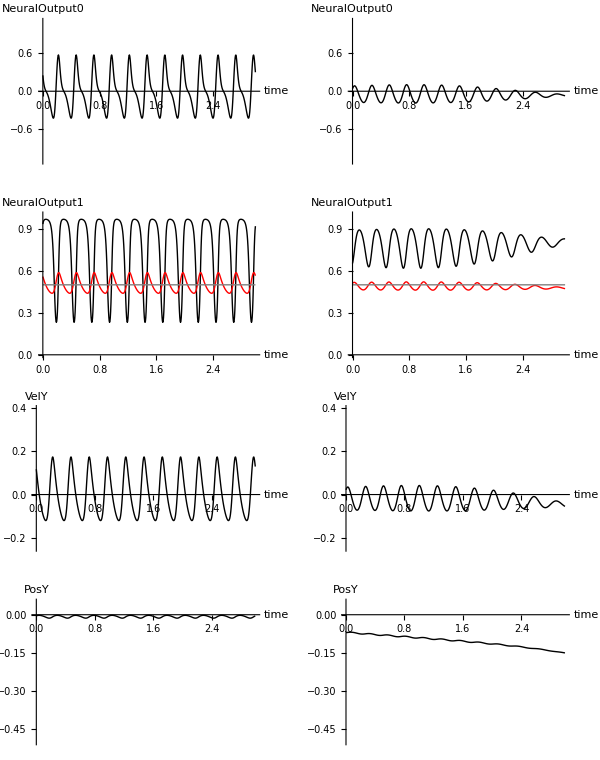

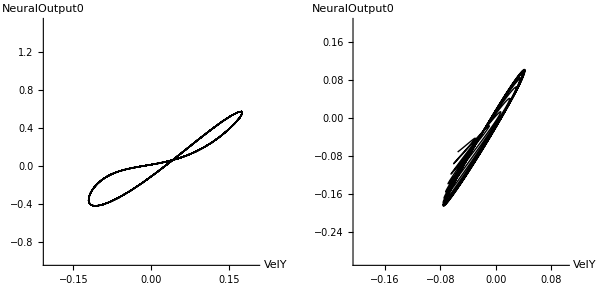

```mathematica
T=10.0; (* trial duration in seconds *)
startAt=7.0;
duration=3.0;
trials={2,12};
SetStartEnd[tr_]:={i0,in}={1+TtoI[trials[[tr]]*T+startAt],TtoI[trials[[tr]]*T+startAt+duration]};

neuralPlotRange={Automatic,{0,1}};
sensorPlotRange={Automatic,{-1.1,1.1}};
velPlotRange={Automatic,{-0.25,0.4}};
posPlotRange={Automatic,{-0.5,0.05}};

AllMaxima[lst_]:=Flatten[Position[Partition[Differences[lst],2,1],{x_,y_}/;Sign[x]>Sign[y]]];
AllMinima[lst_]:=Flatten[Position[Partition[Differences[lst],2,1],{x_,y_}/;Sign[x]<Sign[y]]];
ThreshMax[lst_,t_]:=Cases[AllMaxima[lst]+1,x_/;lst[[x]]>t];
ThreshMin[lst_,t_]:=Cases[AllMaxima[lst]+1,x_/;lst[[x]]<t];

(* Extract minima and maxima *)
SetStartEnd[1];
sensor = NtoD["NeuralOutput0",i0,in];
sensorMaxima=time[[ThreshMax[sensor,0.2]]];
sensorMinima=time[[ThreshMax[sensor,-0.1]]];
maxPoints=Transpose[{sensorMaxima,PadRight[{},Length[sensorMaxima]]}];
minPoints=Transpose[{sensorMinima,PadRight[{},Length[sensorMinima]]}];
maxP=ListPlot[maxPoints,PlotMarkers->{Automatic,8},PlotStyle->Red];
minP=ListPlot[minPoints,PlotMarkers->{Automatic,8}];

(* Plot all relevant state variables *)
options={PlotStyle->Black(*,GridLinesStyle->Dashed,GridLines->{sensorMaxima,{}}*)};
sensorP=Show[TimePlot["NeuralOutput0",i0,in,{options,PlotRange->sensorPlotRange}]];
hiddenP=Show[TimePlot["NeuralOutput1",i0,in,{options,PlotRange->neuralPlotRange}]];
outputP=Show[TimePlot["NeuralOutput2",i0,in,Join[{PlotStyle->Red},options]]];
midLine=ListLinePlot[{{0,0.5},{(in-i0)*dt,0.5}},PlotStyle->{Gray}];
hiddenOutputP=Show[hiddenP,outputP,midLine];
velP=Show[TimePlot["VelY",i0,in,{PlotStyle->Black,PlotRange->velPlotRange}]];
posP=Show[TimePlot["PosY",i0,in,{PlotStyle->Black,PlotRange->posPlotRange}]];

velInPhPlot = PhasePlot["VelY","NeuralOutput0",i0,in,{PlotRange->{{-0.2,0.2},{-1.0,1.5}},AspectRatio->1}];

(* Another trial for comparison *)
SetStartEnd[2];
sensor = NtoD["NeuralOutput0",i0,in];
sensorMaxima=time[[ThreshMax[sensor,0.02]]];
sensorMinima=time[[ThreshMax[sensor,-0.02]]];
maxPoints=Transpose[{sensorMaxima,PadRight[{},Length[sensorMaxima]]}];
minPoints=Transpose[{sensorMinima,PadRight[{},Length[sensorMinima]]}];
maxP=ListPlot[maxPoints,PlotMarkers->{Automatic,8},PlotStyle->Red];
minP=ListPlot[minPoints,PlotMarkers->{Automatic,8}];

options={PlotStyle->Black(*,GridLinesStyle->Dashed,GridLines->{sensorMaxima,{}}*)};
sensorP2=Show[TimePlot["NeuralOutput0",i0,in,{options,PlotRange->sensorPlotRange}]];
hiddenP2=Show[TimePlot["NeuralOutput1",i0,in,{options,PlotRange->neuralPlotRange}]];
outputP2=Show[TimePlot["NeuralOutput2",i0,in,Join[{PlotStyle->Red},options]]];
hiddenOutputP2=Show[hiddenP2,outputP2,midLine];
velP2=Show[TimePlot["VelY",i0,in,{PlotStyle->Black,PlotRange->velPlotRange}]];
posP2=Show[TimePlot["PosY",i0,in,{PlotStyle->Black,PlotRange->posPlotRange}]];

velInPhPlot2 = PhasePlot["VelY","NeuralOutput0",i0,in,{PlotRange->{{-0.2,0.1},{-0.3,0.2}},AspectRatio->1}];

GraphicsGrid[{{sensorP,sensorP2},{hiddenOutputP,hiddenOutputP2},{velP,velP2},{posP,posP2}}, ImageSize->600]
GraphicsGrid[{{velInPhPlot,velInPhPlot2}},ImageSize->600]
```

### SMC: change in perception as function of change in motor command

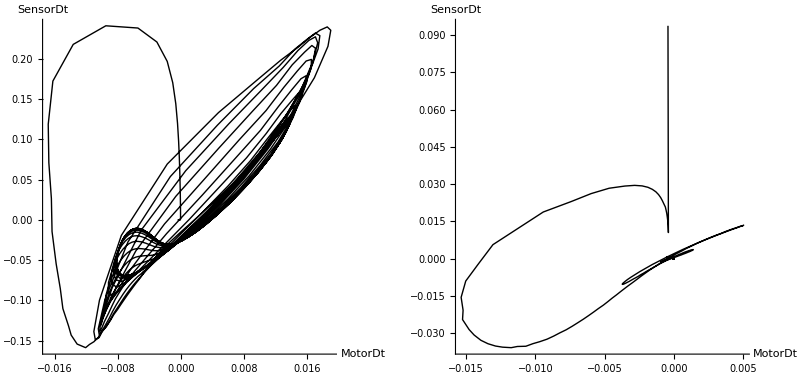

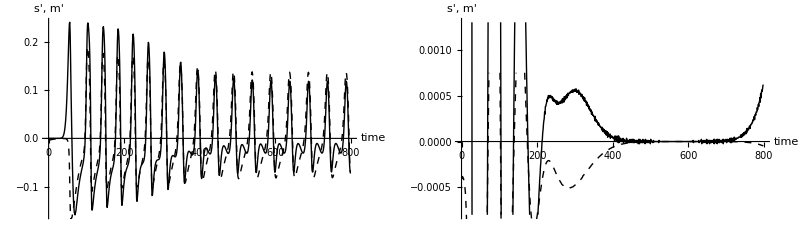

```mathematica
startAt=0;
duration=4;
SetStartEnd[1];
perceptDt=Differences[NtoD["NeuralOutput0",i0,in]];
motorDt=Differences[NtoD["NeuralOutput2",i0,in]];
catchSMCtraj=Transpose[{motorDt,perceptDt}];

catchSMC=Graphics[Line[catchSMCtraj,VertexColors->1-Range[0,1,1/(in-i0)]],Axes->True,AspectRatio->1(*,PlotRange->{{-0.009,0.014},{-0.08,0.13}}*),AxesLabel->{"MotorDt","SensorDt"}];

catchTimePlot=Show[ListLinePlot[perceptDt,PlotStyle->Black],ListLinePlot[10*motorDt,PlotStyle->{Black,Dashed}],AxesLabel->{"time","s', m'"}];

SetStartEnd[2];
perceptDt=Differences[NtoD["NeuralOutput0",i0,in]];
motorDt=Differences[NtoD["NeuralOutput2",i0,in]];
catchSMCtraj=Transpose[{motorDt,perceptDt}];

avoidSMC=Graphics[Line[catchSMCtraj,VertexColors->1-Range[0,1,1/(in-i0)]],Axes->True,AspectRatio->1(*,PlotRange->{{-0.009,0.014},{-0.08,0.13}}*),AxesLabel->{"MotorDt","SensorDt"}];

avoidTimePlot=Show[ListLinePlot[perceptDt,PlotStyle->Black,PlotRange->Automatic],ListLinePlot[motorDt,PlotStyle->{Black,Dashed}],AxesLabel->{"time","s', m'"}];

GraphicsRow[{catchSMC,avoidSMC},ImageSize->800]
GraphicsRow[{catchTimePlot,avoidTimePlot}]
```

Feature: In the catching case, in some region m’ is already positive even though s’ reverses direction for a short amount of time. Presumably, this is because m’ is determined by the motor neuron, which via the hidden neuron, has bistable characteristics. Once a certain threshold (the basin boundary) has been crossed, m’ will move towards positive EP.

## CTRNN Definition

### Differential equations

General definition of the two-node network, and specialization via replacement rules.

```mathematica
σ[x_]=1/(1+ⅇ^-x);

maxp = 30;

neuron= DynamicalSystem[
{(-y+w σ[y+θ]+J)/τ},
{{y,-maxp,maxp}},
{{w,-maxp,maxp},
{θ,-maxp,maxp},
{J,-maxp,maxp},
{τ,0.5,10}}];

couple =DynamicalSystem[
{(-y1+w11 σ[y1+θ1]+w21 σ[y2+θ2]+J)/τ1,(-y2+w12 σ[y1+θ1]+w22 σ[y2+θ2])/τ2},
{{y1,-maxp,maxp},{y2,-maxp,maxp}},
{{w11,-maxp,maxp},{w12,-maxp,maxp},{w21,-maxp,maxp},{w22,-maxp,maxp},{θ1,-maxp,maxp},{θ2,-maxp,maxp},{τ1,0.5,10},{τ2,0.5,10},{J,-maxp,maxp}}];
```

### Specialization

```mathematica
hidden = neuron/.{w->7.54563,θ->-4.0057,τ->1.0,J->0};
output = neuron/.{w->0.0,θ->1.57389,τ->1.0,J->0};
inW=9.79266;

network = couple/.{w11->7.54563,w21->0,w12->-2.07816, w22->0.0,θ1->-4.0057,θ2->1.57389,τ1->1.0,τ2->1.0,J->0};
With[{ε=10^-5},networko=TransformDynamicalSystem[network,{{o1,ε,1-ε},{o2,ε,1-ε}},{σ[y1+θ1],σ[y2+θ2]}]];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

## CTRNN analysis: single node

### Hidden neuron phase portraits

```mathematica
input=-10;
(*DisplayPhasePortrait[hidden/.J->input]
eps=EquilibriumPoints[hidden/.J->input]*)
Manipulate[DisplayPhasePortrait[hidden/.J->input],{input,-10,10}]
```

### Output neuron phase portrait

```mathematica
(*DisplayPhasePortrait[output]
EquilibriumPoints[output]*)
Manipulate[DisplayPhasePortrait[output/.J->Input],{Input,-10,10}]
```

### Hidden neuron bifurcation diagram

DisplayBifurcationDiagram::optx: Unknown option {GridLinesStyle} in {GridLinesStyle → Dashing[{Small, Small}], GridLines → {{0}, {0}}}.

{BifurcationPoint[Fold,{5.68448280810384},{J → -0.674546224845672, w → 7.54563, θ → -4.0057, τ → 1.}],BifurcationPoint[Fold,{2.32691719189616},{J → 1.14031622484567, w → 7.54563, θ → -4.0057, τ → 1.}]}

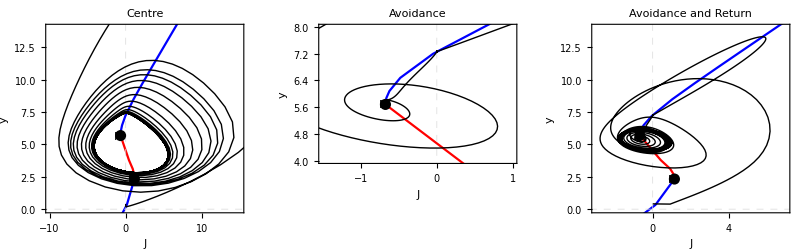

```mathematica
bifPl=DisplayBifurcationDiagram[hidden,J,GridLinesStyle->Dashed,GridLines->{{0},{0}}];
$BifurcationDiagramBPs

(* Overlay actual trajectories *)
duration=5.0;
SetStartEnd[1];
phPlN1F=PhasePlot["NeuralOutput0","NeuralState1",i0,in,{},inW];
phPlN2F=PhasePlot["NeuralOutput0","NeuralState2",i0,in,{},inW];
bifPhPl1=Show[bifPl,phPlN1F,PlotRange->{{-10,15},{0,14}},PlotLabel->"Centre",AspectRatio->1.0];

SetStartEnd[2];
phPlN1A=PhasePlot["NeuralOutput0","NeuralState1",i0,in,{},inW];
phPlN2A=PhasePlot["NeuralOutput0","NeuralState2",i0,in,{},inW];
bifPhPl2=Show[bifPl,phPlN1A,PlotRange->{{-1.5,1},{4,8}},PlotLabel->"Avoidance",AspectRatio->1.0];

(* Show detail of avoidance behaviour, and long-term return to gaussian *)
duration=10.0;SetStartEnd[2];
phPlN1AFull=PhasePlot["NeuralOutput0","NeuralState1",i0,in,{},inW];
bifPhPl2Full=Show[bifPl,phPlN1AFull,PlotRange->{{-3,7},{0,14}},PlotLabel->"Avoidance and Return",AspectRatio->1.0];

GraphicsRow[{bifPhPl1,bifPhPl2,bifPhPl2Full},ImageSize->800]
```

## CTRNN analysis: two-node

### 2d Bifurcation diagram

```mathematica
netBifPl=DisplayBifurcationDiagram[network,J];
$BifurcationDiagramBPs;
bif1J=$BifurcationDiagramBPs[[1,1,9,1,2]]
bif2J=$BifurcationDiagramBPs[[2,1,9,1,2]]

duration=5.0;
SetStartEnd[1];
trjN12FPl=PhasePlot3d["NeuralOutput0","NeuralState1","NeuralState2",i0,in,{},inW];

SetStartEnd[2];
trjN12APl=PhasePlot3d["NeuralOutput0","NeuralState1","NeuralState2",i0,in,{},inW];

range1={{-10,10},{0,10},{-2,0}};
range2={{-3,3},{3,9},{-2.5,-1}};
GraphicsRow[{Show[netBifPl,trjN12FPl,PlotRange->range1],Show[netBifPl,trjN12APl,PlotRange->range2]},ImageSize->800]
```

-0.674546224845672

1.14031622484567

-Graphics-

### Projections

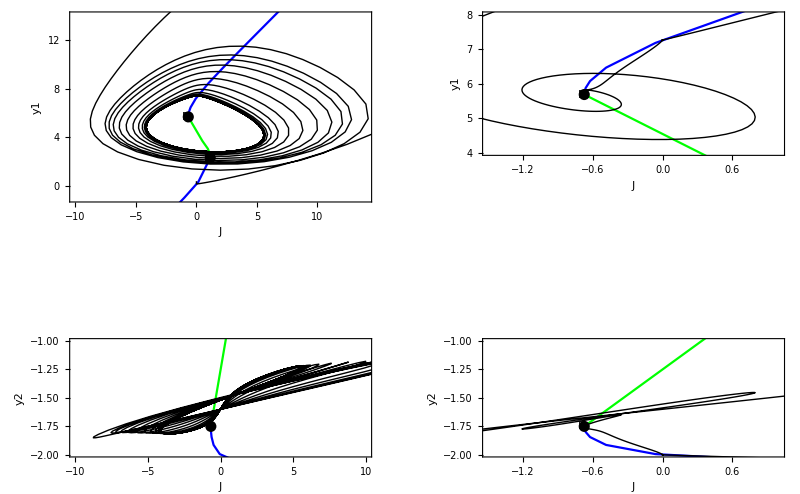

```mathematica
bi1=DisplayBifurcationDiagram[network,J,StateVariables->{y1}];
bi2=DisplayBifurcationDiagram[network,J,StateVariables->{y2}];
phPlY1F=Show[bi1,phPlN1F,PlotRange->{{-10,14},{-1,14}}];
phPlY1A=Show[bi1,phPlN1A,PlotRange->{{-1.5,1},{4,8}}];
phPlY2F=Show[bi2,phPlN2F,PlotRange->{{-10,10},{-2,-1}}];
phPlY2A=Show[bi2,phPlN2A,PlotRange->{{-1.5,1},{-2,-1}}];
GraphicsGrid[{{phPlY1F,phPlY1A},{phPlY2F,phPlY2A}}]
```

### 2d Phase portraits around bifurcation points (in neural output space)

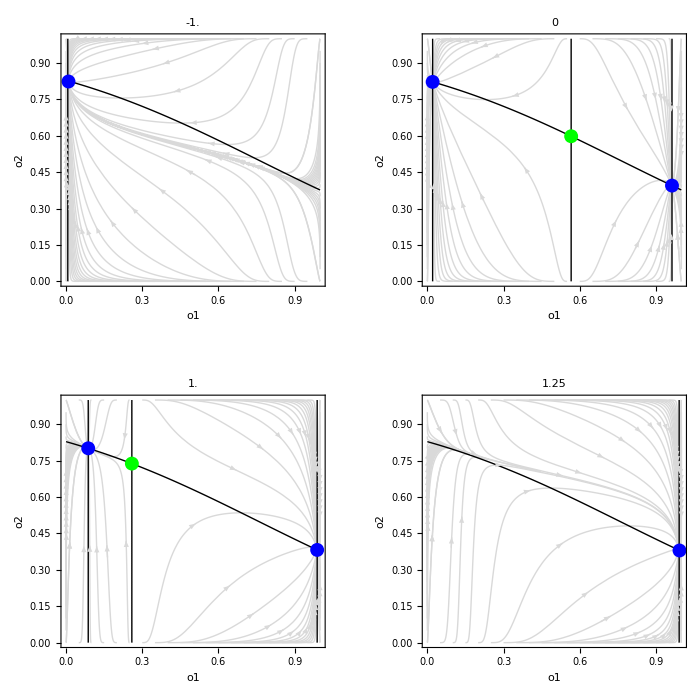

```mathematica
FlowPortrait[input_,dur_:6.0,numPoints_:20]:=Show[DisplayFlow[networko/.J->input,dur,PlotPoints->numPoints,FlowPlotMode->Boundary,PlotStyle->{LightGray}],DisplayPhasePortrait[networko/.J->input,NullManifolds->True,NullManifold2Style->{Black}],PlotLabel->input];

inputs={-1.0,0,1.0,1.25};
flowPortraits=Table[FlowPortrait[x,10.0,20],{x,inputs}];
flowPortraits=Partition[flowPortraits,2];
GraphicsGrid[flowPortraits,ImageSize->700]
```

```mathematica
(*Manipulate[FlowPortrait[input,10,20],{input,-10,10}]*)
```